# Crtanje grafika apsorpcije u sistemu sa cetiri nivoa

```mathematica
(*Clear[S,ro21,dp]

g1=1;
g2=1;
gp=1;
gc=1;

dc=0;
d1=0;
d2=dp+dc-d1;

G32=(g1+gc+gp)/2+I*dc;
G34=(g1+gc+g2)/2+I*d1;
G31=(g1+gc)/2+I*(dp+dc);
G24=(g2+gp)/2+I*(dp-d2);
G21=gp/2+I*dp;
G41=g2/2+I*d2;

fi=0;

rabyc=10;
rabyp=0.05;
raby1=10;
raby2=1;


S = Solve[{-(g1+gc)*ro33-I*rabyc*ro32-I*raby1*ro34+I*rabyc*ro23+I*raby1*ro43 == 0, gc*ro33-gp*ro22+I*rabyc*ro32-I*rabyp*ro21-I*rabyc*ro23+I*rabyp*ro12 == 0, g1*ro33-g2*ro44+I*raby1*ro34-I*raby2*ro41-I*raby1*ro43+I*raby2*ro14 == 0, -G32*ro32-I*rabyc*(ro33-ro22)-I*rabyp*ro31*E^{-I*fi}+I*raby1*ro42 == 0, -G34*ro34-I*raby1*(ro33-ro44)-I*raby2*ro31+I*rabyc*ro24+I*rabyp*ro12 == 0, -G31*ro31-I*rabyp*ro32*E^{-I*fi}-I*raby2*ro34+I*rabyc*ro21*E^{-I*fi}+I*raby1*ro41 == 0, -G24*ro24+I*rabyc*ro34-I*raby2*ro21*E^{-I*fi}-I*raby1*ro23+I*rabyp*ro14*E^{-I*fi} == 0, -G21*ro21-I*rabyp*(ro22-ro11)+I*rabyc*ro31*E^{I*fi}-I*raby2*ro24*E^{I*fi} == 0, -G41*ro41-I*raby2*(ro44-ro11)+I*raby1*ro31-I*rabyp*ro42*E^{-I*fi} == 0, ro11+ro22+ro33+ro44 == 1, ro13 == Conjugate[ro31], ro23 == Conjugate[ro32], ro43 == Conjugate[ro34], ro12 == Conjugate[ro21], ro14 == Conjugate[ro41], ro42 == Conjugate[ro24]},{ro11,ro22,ro33,ro44,ro32,ro34,ro31,ro24,ro21,ro41,ro23,ro43,ro13,ro42,ro12,ro14}][[1]]*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

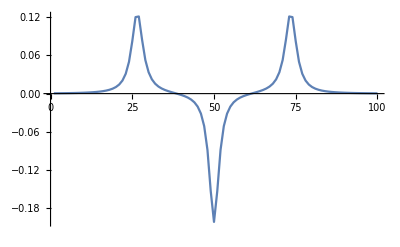

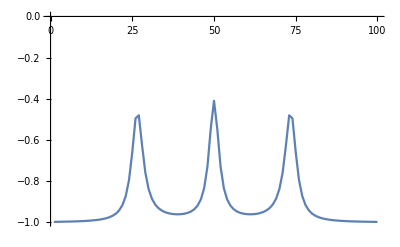

```mathematica
g1=1;
g2=1;
gp=1;
gc=1;

dc=0;
d1=0;

fi=0;

rabyc=10;
rabyp=0.05;
raby1=10;
raby2=1;

Imax=100;
For[i=0,i≤ Imax,i++,
dp=-30+i*60/Imax;

d2=dp+dc-d1;

G32=(g1+gc+gp)/2+I*dc;
G34=(g1+gc+g2)/2+I*d1;
G31=(g1+gc)/2+I*(dp+dc);
G24=(g2+gp)/2+I*(dp-d2);
G21=gp/2+I*dp;
G41=g2/2+I*d2;

S = Solve[{-(g1+gc)*ro33-I*rabyc*ro32-I*raby1*ro34+I*rabyc*ro23+I*raby1*ro43 == 0, gc*ro33-gp*ro22+I*rabyc*ro32-I*rabyp*ro21-I*rabyc*ro23+I*rabyp*ro12 == 0, g1*ro33-g2*ro44+I*raby1*ro34-I*raby2*ro41-I*raby1*ro43+I*raby2*ro14 == 0, -G32*ro32-I*rabyc*(ro33-ro22)-I*rabyp*ro31*E^{-I*fi}+I*raby1*ro42 == 0, -G34*ro34-I*raby1*(ro33-ro44)-I*raby2*ro31+I*rabyc*ro24 == 0, -G31*ro31-I*rabyp*ro32*E^{-I*fi}-I*raby2*ro34+I*rabyc*ro21*E^{-I*fi}+I*raby1*ro41 == 0, -G24*ro24+I*rabyc*ro34-I*raby2*ro21*E^{-I*fi}-I*raby1*ro23+I*rabyp*ro14*E^{-I*fi} == 0, -G21*ro21-I*rabyp*(ro22-ro11)+I*rabyc*ro31*E^{I*fi}-I*raby2*ro24*E^{I*fi} == 0, -G41*ro41-I*raby2*(ro44-ro11)+I*raby1*ro31-I*rabyp*ro42*E^{-I*fi} == 0, ro11+ro22+ro33+ro44 == 1, ro13 == Conjugate[ro31], ro23 == Conjugate[ro32], ro43 == Conjugate[ro34], ro12 == Conjugate[ro21], ro14 == Conjugate[ro41], ro42 == Conjugate[ro24]},{ro11,ro22,ro33,ro44,ro32,ro34,ro31,ro24,ro21,ro41,ro23,ro43,ro13,ro42,ro12,ro14}][[1]];
a[i]=S[[9]][[2]];
b[i]=S[[2]][[2]]-S[[1]][[2]]
]
ListLinePlot[Table[{n,Im[a[n]]},{n,Imax}],PlotRange->All]
ListLinePlot[Table[{n,Re[b[n]]},{n,Imax}],PlotRange->All]
```

```mathematica
ListLinePlot[Table[{n,Im[a[n]]},{n,Imax}],PlotRange->All]
ListLinePlot[Table[{n,Re[b[n]]},{n,Imax}],PlotRange->All]
```

-Graphics-

-Graphics-

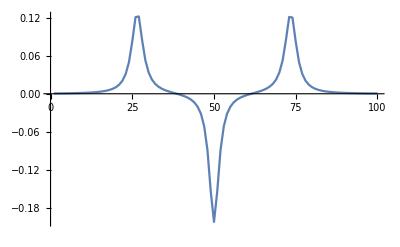

```mathematica
ListLinePlot[Table[{n,Im[a[n]]},{n,Imax}],PlotRange->All]
```

## Naseljenost nivoa

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

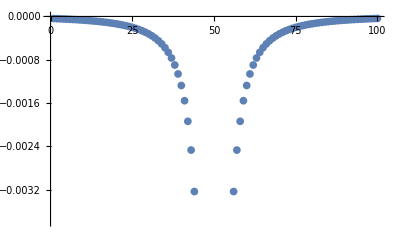

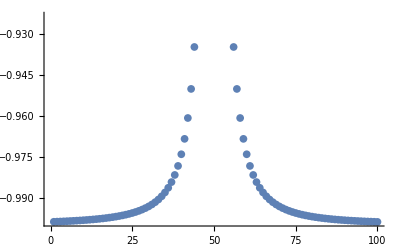

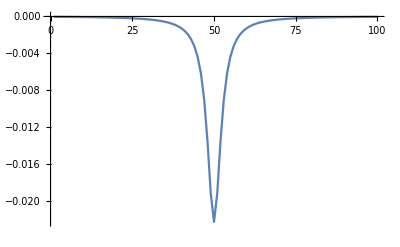

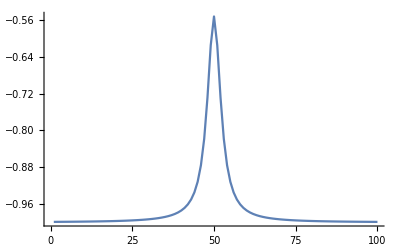

```mathematica
g1=1;
g2=1;
gp=1;
gc=1;

dc=0;
d1=0;

fi=0;

rabyc=100;
rabyp=0.05;
raby1=10;
raby2=1;

Imax=100;
For[i=0,i≤ Imax,i++,
dp=-30+i*60/Imax;

d2=dp+dc-d1;

G32=(g1+gc+gp)/2+I*dc;
G34=(g1+gc+g2)/2+I*d1;
G31=(g1+gc)/2+I*(dp+dc);
G24=(g2+gp)/2+I*(dp-d2);
G21=gp/2+I*dp;
G41=g2/2+I*d2;

S = Solve[{-(g1+gc)*ro33-I*rabyc*ro32-I*raby1*ro34+I*rabyc*ro23+I*raby1*ro43 == 0, gc*ro33-gp*ro22+I*rabyc*ro32-I*rabyp*ro21-I*rabyc*ro23+I*rabyp*ro12 == 0, g1*ro33-g2*ro44+I*raby1*ro34-I*raby2*ro41-I*raby1*ro43+I*raby2*ro14 == 0, -G32*ro32-I*rabyc*(ro33-ro22)-I*rabyp*ro31*E^{-I*fi}+I*raby1*ro42 == 0, -G34*ro34-I*raby1*(ro33-ro44)-I*raby2*ro31+I*rabyc*ro24+I*rabyp*ro12 == 0, -G31*ro31-I*rabyp*ro32*E^{-I*fi}-I*raby2*ro34+I*rabyc*ro21*E^{-I*fi}+I*raby1*ro41 == 0, -G24*ro24+I*rabyc*ro34-I*raby2*ro21*E^{-I*fi}-I*raby1*ro23+I*rabyp*ro14*E^{-I*fi} == 0, -G21*ro21-I*rabyp*(ro22-ro11)+I*rabyc*ro31*E^{I*fi}-I*raby2*ro24*E^{I*fi} == 0, -G41*ro41-I*raby2*(ro44-ro11)+I*raby1*ro31-I*rabyp*ro42*E^{-I*fi} == 0, ro11+ro22+ro33+ro44 == 1, ro13 == Conjugate[ro31], ro23 == Conjugate[ro32], ro43 == Conjugate[ro34], ro12 == Conjugate[ro21], ro14 == Conjugate[ro41], ro42 == Conjugate[ro24]},{ro11,ro22,ro33,ro44,ro32,ro34,ro31,ro24,ro21,ro41,ro23,ro43,ro13,ro42,ro12,ro14}][[1]];
a[i]=S[[9]][[2]];
b[i]=S[[2]][[2]]-S[[1]][[2]]
]
ListLinePlot[Table[{n,Im[a[n]]},{n,Imax}],PlotRange->All]
ListLinePlot[Table[{n,Re[b[n]]},{n,Imax}],PlotRange->All]
```

```mathematica
b[1]
```

(0.000451185-5.20417×10^-18 ⅈ)-ro11

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

```mathematica
g1=1;
g2=1;
gp=1;
gc=1;

dc=0;
d1=0;

fi=π;

rabyc=100;
rabyp=0.05;
raby1=10;
raby2=1;

Imax=100;
For[i=0,i≤ Imax,i++,
dp=-30+i*60/Imax;

d2=dp+dc-d1;

G32=(g1+gc+gp)/2+I*dc;
G34=(g1+gc+g2)/2+I*d1;
G31=(g1+gc)/2+I*(dp+dc);
G24=(g2+gp)/2+I*(dp-d2);
G21=gp/2+I*dp;
G41=g2/2+I*d2;

S = Solve[{-(g1+gc)*ro33-I*rabyc*ro32-I*raby1*ro34+I*rabyc*ro23+I*raby1*ro43 == 0, gc*ro33-gp*ro22+I*rabyc*ro32-I*rabyp*ro21-I*rabyc*ro23+I*rabyp*ro12 == 0, g1*ro33-g2*ro44+I*raby1*ro34-I*raby2*ro41-I*raby1*ro43+I*raby2*ro14 == 0, -G32*ro32-I*rabyc*(ro33-ro22)-I*rabyp*ro31*E^{-I*fi}+I*raby1*ro42 == 0, -G34*ro34-I*raby1*(ro33-ro44)-I*raby2*ro31+I*rabyc*ro24+I*rabyp*ro12 == 0, -G31*ro31-I*rabyp*ro32*E^{-I*fi}-I*raby2*ro34+I*rabyc*ro21*E^{-I*fi}+I*raby1*ro41 == 0, -G24*ro24+I*rabyc*ro34-I*raby2*ro21*E^{-I*fi}-I*raby1*ro23+I*rabyp*ro14*E^{-I*fi} == 0, -G21*ro21-I*rabyp*(ro22-ro11)+I*rabyc*ro31*E^{I*fi}-I*raby2*ro24*E^{I*fi} == 0, -G41*ro41-I*raby2*(ro44-ro11)+I*raby1*ro31-I*rabyp*ro42*E^{-I*fi} == 0, ro11+ro22+ro33+ro44 == 1, ro13 == Conjugate[ro31], ro23 == Conjugate[ro32], ro43 == Conjugate[ro34], ro12 == Conjugate[ro21], ro14 == Conjugate[ro41], ro42 == Conjugate[ro24]},{ro11,ro22,ro33,ro44,ro32,ro34,ro31,ro24,ro21,ro41,ro23,ro43,ro13,ro42,ro12,ro14}][[1]];
a[i]=S[[9]][[2]];
b[i]=S[[2]][[2]]-S[[1]][[2]]
]
ListPlot[Table[{n,Im[a[n]]},{n,Imax}]]
ListPlot[Table[{n,Re[b[n]]},{n,Imax}]]
```